```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["data.xlsx"];
```

```mathematica
plot1=Transpose[{data[[1]][[3;;11,2]],data[[1]][[3;;11,11]]}]
```

{{308.638,4.39788},{320.345,6.72655},{329.37,9.82505},{339.37,13.7844},{348.15,19.2007},{361.077,27.4052},{367.906,34.2057},{377.906,45.0515},{387.418,61.1626}}

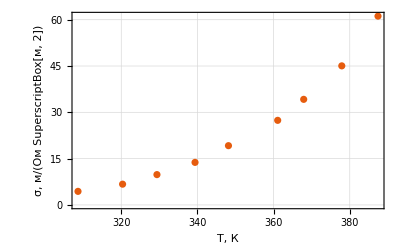

```mathematica
graph1=ListPlot[plot1,PlotTheme->"Scientific",FrameLabel->{"T, К","σ, (:043c)/(:041e:043c SuperscriptBox[:043c, 2])"},GridLines->Automatic]
```

```mathematica
Export["graph1.pdf",graph1]
```

graph1.pdf

```mathematica
plot2=Transpose[{data[[1]][[3;;11,10]],data[[1]][[3;;11,12]]}]
```

{{0.00324004,1.48112},{0.00312163,1.90606},{0.0030361,2.28494},{0.00294664,2.62354},{0.00287233,2.95495},{0.00276949,3.31073},{0.00271808,3.53239},{0.00264616,3.80781},{0.00258119,4.11354}}

```mathematica
graph2Fit=LinearModelFit[plot2,x,x]
```

FittedModel[14.3536-3978.42 x]

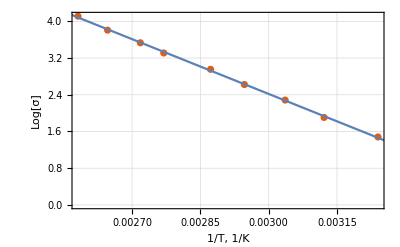

```mathematica
graph2=Show[ListPlot[plot2,PlotTheme->"Scientific",FrameLabel->{"1/T, 1/K", "Log[σ]"},GridLines->Automatic],Plot[graph2Fit["BestFit"],{x,0,1}]]
```

```mathematica
Export["graph2.pdf",graph2]
```

graph2.pdf

```mathematica
k=graph2Fit["BestFitParameters"][[2]]
```

-3978.42

```mathematica
UnitConvert[k*(2Quantity[1,"BoltzmannConstant"])*Quantity[1,"Kelvins"],"Electronvolts"]
```

-0.685667 eV